-Graphics3D-

Piecewise[{{1, x<0}, {0, True}}]

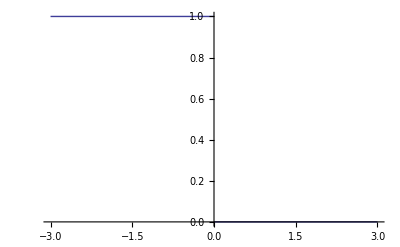

```mathematica
Plot3D[1/(E^(x/t) - 1), 
{x, -10, 10}, {t, 0.0001, 10},
AxesLabel->Automatic,
PlotRange -> Full]
Manipulate[
Plot[
1/(E^(x/t) - 1), 
{x, 0.00001, r},
AxesLabel->Automatic,
PlotRange -> Full],
{{t, 1},0.00001,10},
{{r, 1},1,10}
]
Clear[muZero]
muZero[x_] =
Piecewise[{
{Limit[1/(E^(x/t) + 1), t -> 0,Assumptions->x < 0],x < 0},
{
Limit[1/(E^(x/t) + 1), t -> 0,Assumptions->x > 0],
x > 0}}
]

Plot[
muZero[x], 
{x,-3,3},
AxesLabel->Automatic,
PlotRange->Full]
```